# Miller geometries

## Setting up the relevant equations

First let us note down the parameterization of the flux surface, and we will calculate the Jacobian. These will be used in the rest of the analysis. All the various replacements here are made to highlight that δ, sδ, etc... are all independent variables after our expansion.

```mathematica
Clear["Global`*"]
$Assumptions:={r>0,κ>0,ϵ>0,R0>0}
FortranList={θ->theta,κ->kappa,sκ->skappa,sδ->sdelta,α->alpha,ϵ-> epsilon,q0->q};
```

## Geometry components

```mathematica
Rs=R0[r]+r*Cos[θ+(ArcSin[δ[r]]*Sin[θ])];
Zs=κ[r]*r*Sin[θ];
Jac=FullSimplify[FullSimplify[Rs*(D[Rs,r]*D[Zs,θ]-D[Rs,θ]*D[Zs,r])/.{δ'[r]->sδ*(√(1-δ[r]^2))/r,κ'[r]->sκ*κ/r,R0'[r]->dR0dr}]/.{δ[r]->δ,κ[r]->κ,R0[r]->R0}]/.{ArcSin[δ]->x}
Clear[Rs,Zs]
Rs=R0+r*Cos[θ+(x*Sin[θ])]
Zs=κ*r*Sin[θ]
```

$Aborted

R0+r Cos[θ+x Sin[θ]]

r κ Sin[θ]

```mathematica
FortranForm[FullSimplify[Rs/R0/.{r->R0*ϵ,θ->theta}]]
```

1 + ϵ*Cos(theta + x*Sin(theta))

```mathematica
FortranForm[FullSimplify[Zs/R0/.{r->R0*ϵ,κ->kappa,θ->theta,sκ->skappa,sδ->sdelta}]]
```

kappa*ϵ*Sin(theta)

```mathematica
Rc=FullSimplify[((D[Rs,θ]^2+D[Zs,θ]^2)^(3/2))/(D[Rs,{θ,1}]*D[Zs,{θ,2}]-D[Rs,{θ,2}]*D[Zs,{θ,1}])/.{r->R0*ϵ}]
```

(R0 ϵ (κ^2 Cos[θ]^2+(1+x Cos[θ])^2 Sin[θ+x Sin[θ]]^2)^(3/2))/(κ Cos[θ] (1+x Cos[θ])^2 Cos[θ+x Sin[θ]]+κ Sin[θ] Sin[θ+x Sin[θ]])

```mathematica
FortranForm[Rc/.FortranList]
```

(epsilon*R0*(kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2)**1.5)/
     -  (kappa*Cos(theta)*(1 + x*Cos(theta))**2*Cos(theta + x*Sin(theta)) + kappa*Sin(theta)*Sin(theta + x*Sin(theta)))

```mathematica
sinu=FullSimplify[-D[Zs,θ]*1/(√(D[Zs,θ]^2+D[Rs,θ]^2))]/.{κ->1,x->0}
FortranForm[sinu/.FortranList]
```

-Cos[θ]/(√(Cos[θ]^2+Sin[θ]^2))

-(Cos(theta)/Sqrt(Cos(theta)**2 + Sin(theta)**2))

```mathematica
FortranForm[sinu/.FortranList]
```

-(Cos(theta)/Sqrt(Cos(theta)**2 + Sin(theta)**2))

```mathematica
cosu=FullSimplify[D[Rs,θ]*1/(√(D[Zs,θ]^2+D[Rs,θ]^2))]
```

-((1+x Cos[θ]) Sin[θ+x Sin[θ]])/(√(κ^2 Cos[θ]^2+(1+x Cos[θ])^2 Sin[θ+x Sin[θ]]^2))

```mathematica
FortranForm[cosu/.FortranList]
```

-(((1 + x*Cos(theta))*Sin(theta + x*Sin(theta)))/Sqrt(kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2))

```mathematica
dldθ=FullSimplify[√(D[Zs,θ]^2+D[Rs,θ]^2)/.{r->R0*ϵ}]
```

R0 ϵ √(κ^2 Cos[θ]^2+(1+x Cos[θ])^2 Sin[θ+x Sin[θ]]^2)

```mathematica
FortranForm[dldθ/.FortranList]
```

epsilon*R0*Sqrt(kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2)

## Magnetic field components and stuff

```mathematica
bp=FullSimplify[R0*(√(D[Rs,θ]^2+D[Zs,θ]^2))/Jac/.{r->R0*ϵ,f->B0*R0}]
```

(√(κ^2 Cos[θ]^2+(1+x Cos[θ])^2 Sin[θ+x Sin[θ]]^2))/(κ (1+ϵ Cos[θ+x Sin[θ]]) (Cos[θ] (dR0dr+Cos[θ+x Sin[θ]])+(1+sκ+(-sδ+x+sκ x) Cos[θ]) Sin[θ] Sin[θ+x Sin[θ]]))

```mathematica
FortranForm[bp/.FortranList]
```

Sqrt(kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2)/
     -  (kappa*(1 + epsilon*Cos(theta + x*Sin(theta)))*(Cos(theta)*(dR0dr + Cos(theta + x*Sin(theta))) + 
     -      (1 + skappa + (-sdelta + x + skappa*x)*Cos(theta))*Sin(theta)*Sin(theta + x*Sin(theta))))

```mathematica
bt=FullSimplify[R0/Rs/.{r->R0*ϵ}]
FortranForm[bt/.FortranList]
```

1/(1+ϵ Cos[θ+x Sin[θ]])

1/(1 + epsilon*Cos(theta + x*Sin(theta)))

## Dimensionless constants

```mathematica
Rshat=FullSimplify[Rs/R0/.{r->R0*ϵ}]
dldθhat=FullSimplify[dldθ/r/.{r->R0*ϵ}]
Rchat=FullSimplify[Rc/r/.{r->R0*ϵ}]
```

1+ϵ Cos[θ+x Sin[θ]]

√(κ^2 Cos[θ]^2+(1+x Cos[θ])^2 Sin[θ+x Sin[θ]]^2)

((κ^2 Cos[θ]^2+(1+x Cos[θ])^2 Sin[θ+x Sin[θ]]^2)^(3/2))/(κ Cos[θ] (1+x Cos[θ])^2 Cos[θ+x Sin[θ]]+κ Sin[θ] Sin[θ+x Sin[θ]])

```mathematica
FortranForm[Rchat/.FortranList]
```

(kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2)**1.5/
     -  (kappa*Cos(theta)*(1 + x*Cos(theta))**2*Cos(theta + x*Sin(theta)) + kappa*Sin(theta)*Sin(theta + x*Sin(theta)))

```mathematica
FortranForm[dldθhat/.FortranList]
```

Sqrt(kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2)

```mathematica
γ=FullSimplify[dldθhat/(Rshat^2*bp)]
FortranForm[γ/.FortranList]
```

(κ (Cos[θ] (dR0dr+Cos[θ+x Sin[θ]])+(1+sκ+(-sδ+x+sκ x) Cos[θ]) Sin[θ] Sin[θ+x Sin[θ]]))/(1+ϵ Cos[θ+x Sin[θ]])

(kappa*(Cos(theta)*(dR0dr + Cos(theta + x*Sin(theta))) + (1 + skappa + (-sdelta + x + skappa*x)*Cos(theta))*Sin(theta)*Sin(theta + x*Sin(theta))))/
     -  (1 + epsilon*Cos(theta + x*Sin(theta)))

```mathematica
C1=dldθhat/(Rchat*Rshat^3*bp^2)
FortranForm[C1/.FortranList]
```

(κ^2 (κ Cos[θ] (1+x Cos[θ])^2 Cos[θ+x Sin[θ]]+κ Sin[θ] Sin[θ+x Sin[θ]]) (Cos[θ] (dR0dr+Cos[θ+x Sin[θ]])+(1+sκ+(-sδ+x+sκ x) Cos[θ]) Sin[θ] Sin[θ+x Sin[θ]])^2)/((1+ϵ Cos[θ+x Sin[θ]]) (κ^2 Cos[θ]^2+(1+x Cos[θ])^2 Sin[θ+x Sin[θ]]^2)^2)

(kappa**2*(kappa*Cos(theta)*(1 + x*Cos(theta))**2*Cos(theta + x*Sin(theta)) + kappa*Sin(theta)*Sin(theta + x*Sin(theta)))*
     -    (Cos(theta)*(dR0dr + Cos(theta + x*Sin(theta))) + (1 + skappa + (-sdelta + x + skappa*x)*Cos(theta))*Sin(theta)*Sin(theta + x*Sin(theta)))**2)/
     -  ((1 + epsilon*Cos(theta + x*Sin(theta)))*(kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2)**2)

```mathematica
C2=(dldθhat*sinu)/(Rshat^4*bp^2)
FortranForm[C2/.FortranList]
```

-(κ^2 Cos[θ] (Cos[θ] (dR0dr+Cos[θ+x Sin[θ]])+(1+sκ+(-sδ+x+sκ x) Cos[θ]) Sin[θ] Sin[θ+x Sin[θ]])^2)/((1+ϵ Cos[θ+x Sin[θ]])^2 √(Cos[θ]^2+Sin[θ]^2) √(κ^2 Cos[θ]^2+(1+x Cos[θ])^2 Sin[θ+x Sin[θ]]^2))

-((kappa**2*Cos(theta)*(Cos(theta)*(dR0dr + Cos(theta + x*Sin(theta))) + 
     -         (1 + skappa + (-sdelta + x + skappa*x)*Cos(theta))*Sin(theta)*Sin(theta + x*Sin(theta)))**2)/
     -    ((1 + epsilon*Cos(theta + x*Sin(theta)))**2*Sqrt(Cos(theta)**2 + Sin(theta)**2)*
     -      Sqrt(kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2)))

```mathematica
C3=dldθhat/(Rshat^2*bp^3)
FortranForm[C3/.FortranList]
```

(κ^3 (1+ϵ Cos[θ+x Sin[θ]]) (Cos[θ] (dR0dr+Cos[θ+x Sin[θ]])+(1+sκ+(-sδ+x+sκ x) Cos[θ]) Sin[θ] Sin[θ+x Sin[θ]])^3)/(κ^2 Cos[θ]^2+(1+x Cos[θ])^2 Sin[θ+x Sin[θ]]^2)

(kappa**3*(1 + epsilon*Cos(theta + x*Sin(theta)))*(Cos(theta)*(dR0dr + Cos(theta + x*Sin(theta))) + 
     -       (1 + skappa + (-sdelta + x + skappa*x)*Cos(theta))*Sin(theta)*Sin(theta + x*Sin(theta)))**3)/
     -  (kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2)

```mathematica
C4=dldθhat/(Rshat^3*bp^4)
FortranForm[C4/.FortranList]
```

(κ^4 (1+ϵ Cos[θ+x Sin[θ]]) (Cos[θ] (dR0dr+Cos[θ+x Sin[θ]])+(1+sκ+(-sδ+x+sκ x) Cos[θ]) Sin[θ] Sin[θ+x Sin[θ]])^4)/((κ^2 Cos[θ]^2+(1+x Cos[θ])^2 Sin[θ+x Sin[θ]]^2)^(3/2))

(kappa**4*(1 + epsilon*Cos(theta + x*Sin(theta)))*(Cos(theta)*(dR0dr + Cos(theta + x*Sin(theta))) + 
     -       (1 + skappa + (-sdelta + x + skappa*x)*Cos(theta))*Sin(theta)*Sin(theta + x*Sin(theta)))**4)/
     -  (kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2)**1.5

```mathematica
Clear[γ]
ξ=FortranForm[Simplify[dldθhat*(√(((γ*ϵ)/q)^2*bp^2+bt^2))/bp]/.FortranList]
```

kappa*(1 + epsilon*Cos(theta + x*Sin(theta)))*(Cos(theta)*(dR0dr + Cos(theta + x*Sin(theta))) + 
     -    (1 + skappa + (-sdelta + x + skappa*x)*Cos(theta))*Sin(theta)*Sin(theta + x*Sin(theta)))*
     -  Sqrt((1 + (epsilon**2*γ**2*(kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2))/
     -       (kappa**2*q**2*(Cos(theta)*(dR0dr + Cos(theta + x*Sin(theta))) + (1 + skappa + (-sdelta + x + skappa*x)*Cos(theta))*Sin(theta)*Sin(theta + x*Sin(theta)))**
     -          2))/(1 + epsilon*Cos(theta + x*Sin(theta)))**2)

## Equation for f’(ψ)

```mathematica
Clear[γ,C1,C2,C3,C4]
FortranForm[R0fp/.FullSimplify[Solve[s==(γ*ϵ^2)/q R0fp-2/γ C1-(2ϵ)/γ C2-α/(2γ*ϵ)C3+q/γ^2 R0fp*C4,R0fp]][[1]]/.FortranList]
```

(q*γ*(alpha*C3 + 2*epsilon*(2*C1 + 2*C2*epsilon + s*γ)))/(2.*(C4*epsilon*q**2 + epsilon**3*γ**3))

```mathematica
Simplify[Normal[Series[1-(1+ϵ*Λ)/(1+ϵ*Cos[θ]),{ϵ,0,1}]]]
```

ϵ (-Λ+Cos[θ])

```mathematica
Λsol=Solve[k2==(1-Λ)/2,Λ][[1]]
(λ==1+ϵ*Λ)/.{Λsol}
```

{Λ→1-2 k2}

{λ==1+(1-2 k2) ϵ}

```mathematica
Series[(1+(1-2 k2) ϵ)/(1+ϵ*Cos[θ]),{ϵ,0,1}]
```

1+(1-2 k2-Cos[θ]) ϵ+O[ϵ]^2

```mathematica
Integrate[√(2*k^2-1+Cos[θ])*(s-α*Cos[θ]),{θ,0,p},GenerateConditions->False]
```

-(2 √(-1+2 k^2+Cos[p]) (-√2 (3 s+α-2 k^2 α) EllipticE[p/2,1/k^2]-2 √2 (-1+k^2) α EllipticF[p/2,1/k^2]+α √((-1+2 k^2+Cos[p])/k^2) Sin[p]))/(3 √((-1+2 k^2+Cos[p])/k^2))

```mathematica
FullSimplify[k^2*Limit[Integrate[((1-Sin[ζ]^2)(a+b(1-2*k^2*Sin[ζ]^2)))/(√(1-k^2 Sin[ζ]^2)),{ζ,0,p},GenerateConditions->False],p->π/2]/.{b->3*b3}]
```

(a+b3 (-1+2 k^2)) EllipticE[k^2]+(a-b3) (-1+k^2) EllipticK[k^2]

```mathematica
FullSimplify[Limit[Integrate[(a+b(1-2*k^2*Sin[ζ]^2))/(√(1-k^2 Sin[ζ]^2)),{ζ,0,p},GenerateConditions->False],p->π/2]]
```

2 b EllipticE[k^2]+(a-b) EllipticK[k^2]

```mathematica
Num1=(a+b3 (-1+2 k^2)) EllipticE[k^2]+(a-b3) (-1+k^2) EllipticK[k^2]/.{a->s,b3->-α/3}
Num2=2 b EllipticE[k^2]+(a-b) EllipticK[k^2]/.{a->α/(4*q^2),b->-1/2}
Denom=2 b EllipticE[k^2]+(a-b) EllipticK[k^2]/.{a->1,b->0}
ExpandAll[(2*Num1-Num2)/Denom]
```

(s-1/3 (-1+2 k^2) α) EllipticE[k^2]+(-1+k^2) (s+α/3) EllipticK[k^2]

-EllipticE[k^2]+(1/2+α/(4 q^2)) EllipticK[k^2]

EllipticK[k^2]

-1/2-2 s+2 k^2 s-(2 α)/3+(2 k^2 α)/3-α/(4 q^2)+EllipticE[k^2]/EllipticK[k^2]+(2 s EllipticE[k^2])/EllipticK[k^2]+(2 α EllipticE[k^2])/(3 EllipticK[k^2])-(4 k^2 α EllipticE[k^2])/(3 EllipticK[k^2])

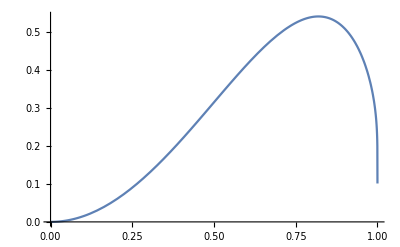

```mathematica
Plot[-(EllipticE[k^2]/EllipticK[k^2]*(2 k^2-1)+1-k^2),{k,0,1}]
```